This is from problem 2M1.
Grid approximation for globe problem.

FIrst make some data, you can choose the parameters and how many flips. 0 is land, 1 is water

```mathematica
data=RandomChoice[{.3,.7}->{0,1},{7}];
```

look at the data.

```mathematica
data
```

{1,1,0,1,1,1,0}

Here we just use Table to go through different values of the parameter and determine the likelihood using PDF[BinomialDistribuiton[...]]. We should then multiply by the prior and normalize, I haven’t done this yet. This is equivalent to having a uniform prior.

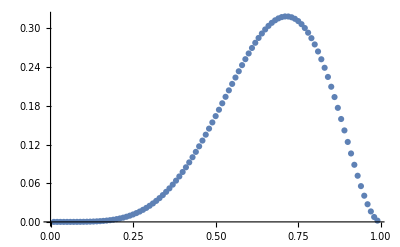

```mathematica
step=0.01;
likelihoodtable=Table[proportionh20 = iter;
ntot=Length[data];
num=Total[data];
likelihood=PDF[BinomialDistribution[ntot,proportionh20],num];
{proportionh20,likelihood}
,{iter,step,1-step,step}];
ListPlot[likelihoodtable]
```